# Hints for a gravitational constant transition in Tully-Fisher data - G. Alestas, I. Antoniou and L. Perivolaropoulos - Figure 5

## General Settings

### Setting the Environment

```mathematica
SetDirectory[NotebookDirectory[]]
Off[General::obspkg,First::nofirst,InterpolatingFunction::dmval,FindMinimum::lstol];
```

### Importing Data

```mathematica
data5=Import["Data//Lel19a2.dat","Data"]
ndat5=Length[data5];
```

{{D631-7,1.76118,0.0308388,8.68,0.05,7.72,0.39,2},{DDO154,1.6721,0.0156979,8.59,0.06,4.04,0.2,2},{DDO161,1.82151,0.0301116,9.32,0.26,7.5,2.25,1},{DDO168,1.72997,0.0299032,8.81,0.06,4.25,0.21,2},{DDO170,1.77815,0.0267633,9.1,0.26,15.4,4.62,1},{ESO079-G014,2.24304,0.011904,10.48,0.24,28.7,7.17,1},{ESO116-G012,2.03782,0.015912,9.55,0.27,13.,3.9,1},{ESO563-G021,2.49776,0.0169682,11.27,0.16,60.8,9.1,1},{F568-V1,2.05038,0.111688,9.72,0.1,80.6,8.06,1},{F571-8,2.1452,0.0180186,9.87,0.19,53.3,10.7,1},{F574-1,1.99034,0.0412699,9.9,0.1,96.8,9.68,1},{F583-1,1.93349,0.0399604,9.52,0.22,35.4,1,8.85},{IC2574,1.82217,0.0392169,9.28,0.06,3.91,0.2,2},{IC4202,2.38489,0.0200363,11.03,0.13,100.4,10.,1},{KK98-251,1.52763,0.0347715,8.29,0.26,6.8,2.04,1},{NGC0024,2.02653,0.0347037,9.45,0.09,7.3,0.36,2},{NGC0055,1.93247,0.0273785,9.64,0.08,2.11,0.11,2},{NGC0100,1.94498,0.0428581,9.63,0.27,18.45,0.2,6},{NGC0247,2.02078,0.0376492,9.78,0.08,3.7,0.19,2},{NGC0289,2.21219,0.0473939,10.86,0.22,20.8,5.2,1},{NGC0300,1.96988,0.0934984,9.43,0.08,2.08,0.1,2},{NGC0801,2.34262,0.0138028,11.27,0.13,80.7,8.07,1},{NGC0891,2.33465,0.0124516,10.88,0.11,9.91,0.5,2},{NGC1003,2.0406,0.0229253,10.05,0.26,11.4,3.42,1},{NGC1090,2.2159,0.0150474,10.68,0.23,37.,9.25,1},{NGC2403,2.11793,0.0201784,9.97,0.08,3.16,0.16,2},{NGC2683,2.18752,0.0321273,10.62,0.11,9.81,0.49,2},{NGC2841,2.45454,0.0233153,11.03,0.13,14.1,1.4,3},{NGC2903,2.26623,0.0176327,10.65,0.28,6.6,1.98,1},{NGC2915,1.92169,0.0415808,9.,0.06,4.06,0.2,2},{NGC2976,1.93146,0.0487869,9.28,0.11,3.58,0.18,2},{NGC2998,2.32201,0.0196427,11.03,0.15,68.1,10.2,1},{NGC3109,1.82086,0.025568,8.86,0.06,1.33,0.07,2},{NGC3198,2.17638,0.0135896,10.53,0.11,13.8,1.4,3},{NGC3521,2.3298,0.0343219,10.68,0.28,7.7,2.3,1},{NGC3726,2.22531,0.0341,10.64,0.15,18.,2.5,4},{NGC3741,1.69984,0.0268543,8.41,0.06,3.21,0.17,2},{NGC3769,2.07408,0.0373255,10.22,0.14,18.,2.5,4},{NGC3877,2.22634,0.0159786,10.58,0.16,18.,2.5,4},{NGC3893,2.24055,0.0364161,10.57,0.15,18.,2.5,4},{NGC3917,2.13322,0.016287,10.13,0.15,18.,2.5,4},{NGC3949,2.21219,0.0428675,10.37,0.15,18.,2.5,4},{NGC3953,2.344,0.0157246,10.87,0.16,18.,2.5,4},{NGC3972,2.12287,0.0176609,9.94,0.15,18.,2.5,4},{NGC3992,2.38202,0.0167477,11.13,0.13,23.7,2.3,5},{NGC4010,2.09968,0.0189746,10.09,0.14,18.,2.5,4},{NGC4013,2.23779,0.0188259,10.64,0.16,18.,2.5,4},{NGC4051,2.1959,0.0301312,10.71,0.16,18.,2.5,4},{NGC4085,2.11893,0.0214525,10.1,0.15,18.,2.5,4},{NGC4088,2.23477,0.0212324,10.81,0.15,18.,2.5,4},{NGC4100,2.19921,0.0224956,10.53,0.15,18.,2.5,4},{NGC4138,2.1682,0.0530346,10.38,0.16,18.,2.5,4},{NGC4157,2.26647,0.0218527,10.8,0.15,18.,2.5,4},{NGC4183,2.04376,0.0258987,10.,0.14,18.,2.5,18.,2.5,4},{NGC4217,2.2584,0.0217838,10.66,0.16,18.,2.5,4},{NGC4559,2.0835,0.0200528,10.24,0.27,7.31,0.2,6},{NGC5005,2.41863,0.0377391,10.96,0.13,16.9,1.5,5},{NGC5033,2.28825,0.0105036,10.85,0.27,15.7,4.7,1},{NGC5055,2.25285,0.0344291,10.96,0.1,9.9,0.5,2},{NGC5371,2.32118,0.0153298,11.27,0.24,39.7,9.92,1},{NGC5585,1.95569,0.0177829,9.57,0.27,7.06,2.12,1},{NGC5907,2.33244,0.0076707,11.06,0.1,17.3,0.9,2},{NGC5985,2.46776,0.0155211,11.08,0.24,50.35,0.2,6},{NGC6015,2.1878,0.0228125,10.38,0.27,17.,5.1,1},{NGC6195,2.40088,0.0260366,11.35,0.13,127.8,12.8,1},{NGC6503,2.06558,0.0123147,9.94,0.09,6.26,0.31,2},{NGC6674,2.38256,0.0343531,11.18,0.19,51.2,10.2,1},{NGC6946,2.20112,0.0404229,10.61,0.28,5.52,1.66,2},{NGC7331,2.3784,0.0112586,11.15,0.13,14.7,1.5,3},{NGC7814,2.34025,0.014275,10.59,0.11,14.4,0.72,2},{UGC00128,2.11261,0.0502315,10.2,0.14,64.5,9.7,1},{UGC00731,1.8651,0.0236835,9.41,0.26,12.5,3.75,1},{UGC01281,1.74194,0.0330217,8.75,0.06,5.27,0.1,6},{UGC02259,1.93551,0.0312158,9.18,0.26,10.5,3.1,1},{UGC02487,2.52114,0.0533349,11.43,0.16,69.1,10.4,1},{UGC02885,2.46165,0.0238363,11.41,0.12,80.6,8.06,1},{UGC02916,2.26174,0.0410958,10.97,0.15,65.4,9.8,1},{UGC02953,2.42308,0.0273605,11.15,0.28,16.5,4.95,1},{UGC03205,2.34163,0.0215419,10.84,0.2,50.,10.,1},{UGC03546,2.29425,0.0337237,10.73,0.24,28.7,7.2,1},{UGC03580,2.10106,0.0192583,10.09,0.23,20.7,5.2,1},{UGC04278,1.96095,0.034663,9.33,0.26,12.59,0.2,6},{UGC04325,1.95856,0.0305567,9.28,0.27,9.6,2.88,1},{UGC04499,1.86213,0.0262308,9.35,0.26,12.5,3.75,1},{UGC05253,2.3298,0.0434609,11.03,0.23,22.9,5.72,1},{UGC05716,1.86392,0.0558085,9.24,0.22,21.3,5.3,1},{UGC05721,1.90146,0.0424743,9.01,0.26,6.18,1.85,1},{UGC05986,2.05308,0.0188195,9.77,0.27,8.63,2.59,1},{UGC06399,1.92942,0.0265506,9.31,0.14,18.,2.5,4},{UGC06446,1.91487,0.0369586,9.37,0.26,12.,3.6,1},{UGC06614,2.3006,0.11165,10.96,0.12,88.7,8.87,1},{UGC06667,1.92324,0.0201981,9.25,0.13,18.,2.5,4},{UGC06786,2.34124,0.0193856,10.64,0.24,29.3,7.32,1},{UGC06787,2.39463,0.0134696,10.75,0.24,21.3,5.32,1},{UGC06818,1.85248,0.0390112,9.35,0.13,18.,2.5,4},{UGC06917,2.03623,0.0247544,9.79,0.14,18.,2.5,4},{UGC06923,1.90091,0.0278065,9.4,0.14,18.,2.5,4},{UGC06930,2.03019,0.0663955,9.94,0.13,18.,2.5,4},{UGC06983,2.03743,0.0310569,9.82,0.13,18.,2.5,4},{UGC07125,1.81425,0.018638,9.88,0.26,19.8,5.9,1},{UGC07151,1.86629,0.0218476,9.29,0.08,6.87,0.34,2},{UGC07399,2.01284,0.026967,9.2,0.27,8.43,2.53,1},{UGC07524,1.90091,0.0310779,9.55,0.06,4.74,0.24,2},{UGC07603,1.78958,0.02325,8.73,0.26,4.7,1.41,1},{UGC07690,1.75891,0.0551951,8.98,0.27,8.11,2.43,1},{UGC08286,1.91593,0.0131675,9.17,0.06,6.5,0.33,2},{UGC08490,1.89542,0.0287125,9.17,0.11,4.65,0.53,2},{UGC08550,1.75511,0.0175431,8.72,0.26,6.7,2.,1},{UGC08699,2.26102,0.0268871,10.48,0.24,39.3,9.82,1},{UGC09037,2.1827,0.0424596,10.78,0.11,83.6,8.4,1},{UGC09133,2.35564,0.0352099,11.27,0.19,57.1,11.4,1},{UGC10310,1.8537,0.0747647,9.39,0.27,15.2,4.6,1},{UGC11455,2.4304,0.013049,11.31,0.16,78.6,11.8,1},{UGC11914,2.45954,0.0650774,10.88,0.28,16.9,5.1,1},{UGC12506,2.36922,0.0324573,11.07,0.11,100.6,10.1,1},{UGC12632,1.85552,0.0296597,9.47,0.26,9.77,2.93,1},{UGCA442,1.75128,0.0323191,8.62,0.06,4.35,0.22,2},{UGCA444,1.5682,0.0738973,7.98,0.06,0.98,0.05,2}}

```mathematica
data5[[1,6]]
```

7.72

```mathematica
dchi[nsig_,M_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]//N
```

```mathematica
test1=Table[{data5[[i,6]],data5[[i,7]],data5[[i,2]],data5[[i,3]],data5[[i,4]],data5[[i,5]],data5[[i,8]]},{i,1,ndat5}]
```

{{7.72,0.39,1.76118,0.0308388,8.68,0.05,2},{4.04,0.2,1.6721,0.0156979,8.59,0.06,2},{7.5,2.25,1.82151,0.0301116,9.32,0.26,1},{4.25,0.21,1.72997,0.0299032,8.81,0.06,2},{15.4,4.62,1.77815,0.0267633,9.1,0.26,1},{28.7,7.17,2.24304,0.011904,10.48,0.24,1},{13.,3.9,2.03782,0.015912,9.55,0.27,1},{60.8,9.1,2.49776,0.0169682,11.27,0.16,1},{80.6,8.06,2.05038,0.111688,9.72,0.1,1},{53.3,10.7,2.1452,0.0180186,9.87,0.19,1},{96.8,9.68,1.99034,0.0412699,9.9,0.1,1},{35.4,1,1.93349,0.0399604,9.52,0.22,8.85},{3.91,0.2,1.82217,0.0392169,9.28,0.06,2},{100.4,10.,2.38489,0.0200363,11.03,0.13,1},{6.8,2.04,1.52763,0.0347715,8.29,0.26,1},{7.3,0.36,2.02653,0.0347037,9.45,0.09,2},{2.11,0.11,1.93247,0.0273785,9.64,0.08,2},{18.45,0.2,1.94498,0.0428581,9.63,0.27,6},{3.7,0.19,2.02078,0.0376492,9.78,0.08,2},{20.8,5.2,2.21219,0.0473939,10.86,0.22,1},{2.08,0.1,1.96988,0.0934984,9.43,0.08,2},{80.7,8.07,2.34262,0.0138028,11.27,0.13,1},{9.91,0.5,2.33465,0.0124516,10.88,0.11,2},{11.4,3.42,2.0406,0.0229253,10.05,0.26,1},{37.,9.25,2.2159,0.0150474,10.68,0.23,1},{3.16,0.16,2.11793,0.0201784,9.97,0.08,2},{9.81,0.49,2.18752,0.0321273,10.62,0.11,2},{14.1,1.4,2.45454,0.0233153,11.03,0.13,3},{6.6,1.98,2.26623,0.0176327,10.65,0.28,1},{4.06,0.2,1.92169,0.0415808,9.,0.06,2},{3.58,0.18,1.93146,0.0487869,9.28,0.11,2},{68.1,10.2,2.32201,0.0196427,11.03,0.15,1},{1.33,0.07,1.82086,0.025568,8.86,0.06,2},{13.8,1.4,2.17638,0.0135896,10.53,0.11,3},{7.7,2.3,2.3298,0.0343219,10.68,0.28,1},{18.,2.5,2.22531,0.0341,10.64,0.15,4},{3.21,0.17,1.69984,0.0268543,8.41,0.06,2},{18.,2.5,2.07408,0.0373255,10.22,0.14,4},{18.,2.5,2.22634,0.0159786,10.58,0.16,4},{18.,2.5,2.24055,0.0364161,10.57,0.15,4},{18.,2.5,2.13322,0.016287,10.13,0.15,4},{18.,2.5,2.21219,0.0428675,10.37,0.15,4},{18.,2.5,2.344,0.0157246,10.87,0.16,4},{18.,2.5,2.12287,0.0176609,9.94,0.15,4},{23.7,2.3,2.38202,0.0167477,11.13,0.13,5},{18.,2.5,2.09968,0.0189746,10.09,0.14,4},{18.,2.5,2.23779,0.0188259,10.64,0.16,4},{18.,2.5,2.1959,0.0301312,10.71,0.16,4},{18.,2.5,2.11893,0.0214525,10.1,0.15,4},{18.,2.5,2.23477,0.0212324,10.81,0.15,4},{18.,2.5,2.19921,0.0224956,10.53,0.15,4},{18.,2.5,2.1682,0.0530346,10.38,0.16,4},{18.,2.5,2.26647,0.0218527,10.8,0.15,4},{18.,2.5,2.04376,0.0258987,10.,0.14,18.},{18.,2.5,2.2584,0.0217838,10.66,0.16,4},{7.31,0.2,2.0835,0.0200528,10.24,0.27,6},{16.9,1.5,2.41863,0.0377391,10.96,0.13,5},{15.7,4.7,2.28825,0.0105036,10.85,0.27,1},{9.9,0.5,2.25285,0.0344291,10.96,0.1,2},{39.7,9.92,2.32118,0.0153298,11.27,0.24,1},{7.06,2.12,1.95569,0.0177829,9.57,0.27,1},{17.3,0.9,2.33244,0.0076707,11.06,0.1,2},{50.35,0.2,2.46776,0.0155211,11.08,0.24,6},{17.,5.1,2.1878,0.0228125,10.38,0.27,1},{127.8,12.8,2.40088,0.0260366,11.35,0.13,1},{6.26,0.31,2.06558,0.0123147,9.94,0.09,2},{51.2,10.2,2.38256,0.0343531,11.18,0.19,1},{5.52,1.66,2.20112,0.0404229,10.61,0.28,2},{14.7,1.5,2.3784,0.0112586,11.15,0.13,3},{14.4,0.72,2.34025,0.014275,10.59,0.11,2},{64.5,9.7,2.11261,0.0502315,10.2,0.14,1},{12.5,3.75,1.8651,0.0236835,9.41,0.26,1},{5.27,0.1,1.74194,0.0330217,8.75,0.06,6},{10.5,3.1,1.93551,0.0312158,9.18,0.26,1},{69.1,10.4,2.52114,0.0533349,11.43,0.16,1},{80.6,8.06,2.46165,0.0238363,11.41,0.12,1},{65.4,9.8,2.26174,0.0410958,10.97,0.15,1},{16.5,4.95,2.42308,0.0273605,11.15,0.28,1},{50.,10.,2.34163,0.0215419,10.84,0.2,1},{28.7,7.2,2.29425,0.0337237,10.73,0.24,1},{20.7,5.2,2.10106,0.0192583,10.09,0.23,1},{12.59,0.2,1.96095,0.034663,9.33,0.26,6},{9.6,2.88,1.95856,0.0305567,9.28,0.27,1},{12.5,3.75,1.86213,0.0262308,9.35,0.26,1},{22.9,5.72,2.3298,0.0434609,11.03,0.23,1},{21.3,5.3,1.86392,0.0558085,9.24,0.22,1},{6.18,1.85,1.90146,0.0424743,9.01,0.26,1},{8.63,2.59,2.05308,0.0188195,9.77,0.27,1},{18.,2.5,1.92942,0.0265506,9.31,0.14,4},{12.,3.6,1.91487,0.0369586,9.37,0.26,1},{88.7,8.87,2.3006,0.11165,10.96,0.12,1},{18.,2.5,1.92324,0.0201981,9.25,0.13,4},{29.3,7.32,2.34124,0.0193856,10.64,0.24,1},{21.3,5.32,2.39463,0.0134696,10.75,0.24,1},{18.,2.5,1.85248,0.0390112,9.35,0.13,4},{18.,2.5,2.03623,0.0247544,9.79,0.14,4},{18.,2.5,1.90091,0.0278065,9.4,0.14,4},{18.,2.5,2.03019,0.0663955,9.94,0.13,4},{18.,2.5,2.03743,0.0310569,9.82,0.13,4},{19.8,5.9,1.81425,0.018638,9.88,0.26,1},{6.87,0.34,1.86629,0.0218476,9.29,0.08,2},{8.43,2.53,2.01284,0.026967,9.2,0.27,1},{4.74,0.24,1.90091,0.0310779,9.55,0.06,2},{4.7,1.41,1.78958,0.02325,8.73,0.26,1},{8.11,2.43,1.75891,0.0551951,8.98,0.27,1},{6.5,0.33,1.91593,0.0131675,9.17,0.06,2},{4.65,0.53,1.89542,0.0287125,9.17,0.11,2},{6.7,2.,1.75511,0.0175431,8.72,0.26,1},{39.3,9.82,2.26102,0.0268871,10.48,0.24,1},{83.6,8.4,2.1827,0.0424596,10.78,0.11,1},{57.1,11.4,2.35564,0.0352099,11.27,0.19,1},{15.2,4.6,1.8537,0.0747647,9.39,0.27,1},{78.6,11.8,2.4304,0.013049,11.31,0.16,1},{16.9,5.1,2.45954,0.0650774,10.88,0.28,1},{100.6,10.1,2.36922,0.0324573,11.07,0.11,1},{9.77,2.93,1.85552,0.0296597,9.47,0.26,1},{4.35,0.22,1.75128,0.0323191,8.62,0.06,2},{0.98,0.05,1.5682,0.0738973,7.98,0.06,2}}

```mathematica
tests9=Select[test1,#[[1]]<9 &];
testl9=Select[test1,#[[1]]>9 &];
tests17=Select[test1,#[[1]]<17 &];
testl17=Select[test1,#[[1]]>17 &];
tests20=Select[test1,#[[1]]<20 &];
testl20=Select[test1,#[[1]]>20 &];
```

```mathematica
emcee9s=Table[{tests9[[i,3]],tests9[[i,5]],tests9[[i,4]],tests9[[i,6]]},{i,1,Length[tests9]}];
emcee9l=Table[{testl9[[i,3]],testl9[[i,5]],testl9[[i,4]],testl9[[i,6]]},{i,1,Length[testl9]}];
emcee17s=Table[{tests17[[i,3]],tests17[[i,5]],tests17[[i,4]],tests17[[i,6]]},{i,1,Length[tests17]}];
emcee17l=Table[{testl17[[i,3]],testl17[[i,5]],testl17[[i,4]],testl17[[i,6]]},{i,1,Length[testl17]}];
emcee20s=Table[{tests20[[i,3]],tests20[[i,5]],tests20[[i,4]],tests20[[i,6]]},{i,1,Length[tests20]}];
emcee20l=Table[{testl20[[i,3]],testl20[[i,5]],testl20[[i,4]],testl20[[i,6]]},{i,1,Length[testl20]}];
emceeall=Table[{test1[[i,3]],test1[[i,5]],test1[[i,4]],test1[[i,6]]},{i,1,Length[test1]}];
```

```mathematica
Export["Lel19_9s.dat",emcee9s]
Export["Lel19_9l.dat",emcee9l]
Export["Lel19_17s.dat",emcee17s]
Export["Lel19_17l.dat",emcee17l]
Export["Lel19_20s.dat",emcee20s]
Export["Lel19_20l.dat",emcee20l]
Export["Lel19all.dat",emceeall]
```

Lel19_9s.dat

Lel19_9l.dat

Lel19_17s.dat

Lel19_17l.dat

Lel19_20s.dat

Lel19_20l.dat

Lel19all.dat

```mathematica
test1r=Table[{RandomVariate[NormalDistribution[data5[[i,6]],data5[[i,7]]]],data5[[i,7]],data5[[i,2]],data5[[i,3]],data5[[i,4]]+0.05,data5[[i,5]]},{i,1,ndat5}]
```

{{8.20935,0.39,1.76118,0.0308388,8.73,0.05},{4.05258,0.2,1.6721,0.0156979,8.64,0.06},{5.45503,2.25,1.82151,0.0301116,9.37,0.26},{4.36799,0.21,1.72997,0.0299032,8.86,0.06},{7.46965,4.62,1.77815,0.0267633,9.15,0.26},{30.371,7.17,2.24304,0.011904,10.53,0.24},{18.5134,3.9,2.03782,0.015912,9.6,0.27},{73.5869,9.1,2.49776,0.0169682,11.32,0.16},{79.7196,8.06,2.05038,0.111688,9.77,0.1},{65.8779,10.7,2.1452,0.0180186,9.92,0.19},{111.742,9.68,1.99034,0.0412699,9.95,0.1},{40.9178,8.85,1.93349,0.0399604,9.57,0.22},{3.7337,0.2,1.82217,0.0392169,9.33,0.06},{82.3702,10.,2.38489,0.0200363,11.08,0.13},{6.99102,2.04,1.52763,0.0347715,8.34,0.26},{7.12259,0.36,2.02653,0.0347037,9.5,0.09},{2.07968,0.11,1.93247,0.0273785,9.69,0.08},{18.4825,0.2,1.94498,0.0428581,9.68,0.27},{3.89643,0.19,2.02078,0.0376492,9.83,0.08},{17.9108,5.2,2.21219,0.0473939,10.91,0.22},{2.13413,0.1,1.96988,0.0934984,9.48,0.08},{68.2334,8.07,2.34262,0.0138028,11.32,0.13},{10.6817,0.5,2.33465,0.0124516,10.93,0.11},{12.8792,3.42,2.0406,0.0229253,10.1,0.26},{35.4729,9.25,2.2159,0.0150474,10.73,0.23},{3.43461,0.16,2.11793,0.0201784,10.02,0.08},{8.96525,0.49,2.18752,0.0321273,10.67,0.11},{14.3759,1.4,2.45454,0.0233153,11.08,0.13},{5.44287,1.98,2.26623,0.0176327,10.7,0.28},{4.30178,0.2,1.92169,0.0415808,9.05,0.06},{3.36768,0.18,1.93146,0.0487869,9.33,0.11},{72.1425,10.2,2.32201,0.0196427,11.08,0.15},{1.3324,0.07,1.82086,0.025568,8.91,0.06},{14.2097,1.4,2.17638,0.0135896,10.58,0.11},{7.65501,2.3,2.3298,0.0343219,10.73,0.28},{18.6175,2.5,2.22531,0.0341,10.69,0.15},{3.27129,0.17,1.69984,0.0268543,8.46,0.06},{19.2707,2.5,2.07408,0.0373255,10.27,0.14},{19.3694,2.5,2.22634,0.0159786,10.63,0.16},{14.6491,2.5,2.24055,0.0364161,10.62,0.15},{18.6447,2.5,2.13322,0.016287,10.18,0.15},{14.6971,2.5,2.21219,0.0428675,10.42,0.15},{19.7584,2.5,2.344,0.0157246,10.92,0.16},{18.296,2.5,2.12287,0.0176609,9.99,0.15},{18.0012,2.3,2.38202,0.0167477,11.18,0.13},{19.0006,2.5,2.09968,0.0189746,10.14,0.14},{19.8904,2.5,2.23779,0.0188259,10.69,0.16},{19.3567,2.5,2.1959,0.0301312,10.76,0.16},{16.9987,2.5,2.11893,0.0214525,10.15,0.15},{17.9227,2.5,2.23477,0.0212324,10.86,0.15},{13.7675,2.5,2.19921,0.0224956,10.58,0.15},{20.5079,2.5,2.1682,0.0530346,10.43,0.16},{20.4176,2.5,2.26647,0.0218527,10.85,0.15},{21.673,2.5,2.04376,0.0258987,10.05,0.14},{23.167,2.5,2.2584,0.0217838,10.71,0.16},{7.15438,0.2,2.0835,0.0200528,10.29,0.27},{16.5646,1.5,2.41863,0.0377391,11.01,0.13},{10.414,4.7,2.28825,0.0105036,10.9,0.27},{10.3962,0.5,2.25285,0.0344291,11.01,0.1},{38.7897,9.92,2.32118,0.0153298,11.32,0.24},{11.2799,2.12,1.95569,0.0177829,9.62,0.27},{18.3289,0.9,2.33244,0.0076707,11.11,0.1},{50.2098,0.2,2.46776,0.0155211,11.13,0.24},{12.4005,5.1,2.1878,0.0228125,10.43,0.27},{145.504,12.8,2.40088,0.0260366,11.4,0.13},{6.22187,0.31,2.06558,0.0123147,9.99,0.09},{46.8594,10.2,2.38256,0.0343531,11.23,0.19},{4.16533,1.66,2.20112,0.0404229,10.66,0.28},{13.8759,1.5,2.3784,0.0112586,11.2,0.13},{14.1089,0.72,2.34025,0.014275,10.64,0.11},{63.9398,9.7,2.11261,0.0502315,10.25,0.14},{14.3695,3.75,1.8651,0.0236835,9.46,0.26},{5.13821,0.1,1.74194,0.0330217,8.8,0.06},{9.46262,3.1,1.93551,0.0312158,9.23,0.26},{76.3599,10.4,2.52114,0.0533349,11.48,0.16},{82.0592,8.06,2.46165,0.0238363,11.46,0.12},{68.1501,9.8,2.26174,0.0410958,11.02,0.15},{14.0898,4.95,2.42308,0.0273605,11.2,0.28},{55.0134,10.,2.34163,0.0215419,10.89,0.2},{35.4487,7.2,2.29425,0.0337237,10.78,0.24},{24.3098,5.2,2.10106,0.0192583,10.14,0.23},{12.3498,0.2,1.96095,0.034663,9.38,0.26},{9.38279,2.88,1.95856,0.0305567,9.33,0.27},{5.1421,3.75,1.86213,0.0262308,9.4,0.26},{23.3723,5.72,2.3298,0.0434609,11.08,0.23},{28.5049,5.3,1.86392,0.0558085,9.29,0.22},{8.8441,1.85,1.90146,0.0424743,9.06,0.26},{6.30319,2.59,2.05308,0.0188195,9.82,0.27},{22.3619,2.5,1.92942,0.0265506,9.36,0.14},{20.2602,3.6,1.91487,0.0369586,9.42,0.26},{81.2904,8.87,2.3006,0.11165,11.01,0.12},{15.1759,2.5,1.92324,0.0201981,9.3,0.13},{41.7055,7.32,2.34124,0.0193856,10.69,0.24},{25.4901,5.32,2.39463,0.0134696,10.8,0.24},{16.232,2.5,1.85248,0.0390112,9.4,0.13},{17.9849,2.5,2.03623,0.0247544,9.84,0.14},{14.7169,2.5,1.90091,0.0278065,9.45,0.14},{21.8786,2.5,2.03019,0.0663955,9.99,0.13},{17.4111,2.5,2.03743,0.0310569,9.87,0.13},{14.3843,5.9,1.81425,0.018638,9.93,0.26},{6.82673,0.34,1.86629,0.0218476,9.34,0.08},{10.34,2.53,2.01284,0.026967,9.25,0.27},{4.6377,0.24,1.90091,0.0310779,9.6,0.06},{2.4624,1.41,1.78958,0.02325,8.78,0.26},{6.25052,2.43,1.75891,0.0551951,9.03,0.27},{6.93973,0.33,1.91593,0.0131675,9.22,0.06},{4.84085,0.53,1.89542,0.0287125,9.22,0.11},{7.78759,2.,1.75511,0.0175431,8.77,0.26},{53.026,9.82,2.26102,0.0268871,10.53,0.24},{83.4834,8.4,2.1827,0.0424596,10.83,0.11},{61.0862,11.4,2.35564,0.0352099,11.32,0.19},{20.2539,4.6,1.8537,0.0747647,9.44,0.27},{92.0818,11.8,2.4304,0.013049,11.36,0.16},{27.6636,5.1,2.45954,0.0650774,10.93,0.28},{86.257,10.1,2.36922,0.0324573,11.12,0.11},{13.1777,2.93,1.85552,0.0296597,9.52,0.26},{4.14573,0.22,1.75128,0.0323191,8.67,0.06},{0.951958,0.05,1.5682,0.0738973,8.03,0.06}}

```mathematica
data5[[1,7]]
```

0.39

```mathematica
Table[If[data5[[i,6]]>18,{RandomVariate[NormalDistribution[data5[[i,6]],data5[[i,7]]]],data5[[i,7]],data5[[i,2]],data5[[i,3]],data5[[i,4]]+0.05,data5[[i,5]]},{RandomVariate[NormalDistribution[data5[[i,6]],data5[[i,7]]]],data5[[i,7]],data5[[i,2]],data5[[i,3]],data5[[i,4]],data5[[i,5]]}],{i,1,ndat5}]
```

{{7.84783,0.39,1.76118,0.0308388,8.68,0.05},{4.05113,0.2,1.6721,0.0156979,8.59,0.06},{11.8229,2.25,1.82151,0.0301116,9.32,0.26},{4.14033,0.21,1.72997,0.0299032,8.81,0.06},{8.80253,4.62,1.77815,0.0267633,9.1,0.26},{23.881,7.17,2.24304,0.011904,10.53,0.24},{14.259,3.9,2.03782,0.015912,9.55,0.27},{67.6452,9.1,2.49776,0.0169682,11.32,0.16},{78.3094,8.06,2.05038,0.111688,9.77,0.1},{64.0319,10.7,2.1452,0.0180186,9.92,0.19},{86.7475,9.68,1.99034,0.0412699,9.95,0.1},{18.1598,8.85,1.93349,0.0399604,9.57,0.22},{4.05321,0.2,1.82217,0.0392169,9.28,0.06},{102.373,10.,2.38489,0.0200363,11.08,0.13},{6.0096,2.04,1.52763,0.0347715,8.29,0.26},{7.46324,0.36,2.02653,0.0347037,9.45,0.09},{2.00761,0.11,1.93247,0.0273785,9.64,0.08},{18.5072,0.2,1.94498,0.0428581,9.68,0.27},{3.77167,0.19,2.02078,0.0376492,9.78,0.08},{17.6519,5.2,2.21219,0.0473939,10.91,0.22},{2.10065,0.1,1.96988,0.0934984,9.43,0.08},{81.7313,8.07,2.34262,0.0138028,11.32,0.13},{9.64492,0.5,2.33465,0.0124516,10.88,0.11},{16.6186,3.42,2.0406,0.0229253,10.05,0.26},{24.5291,9.25,2.2159,0.0150474,10.73,0.23},{2.89545,0.16,2.11793,0.0201784,9.97,0.08},{9.52644,0.49,2.18752,0.0321273,10.62,0.11},{13.9445,1.4,2.45454,0.0233153,11.03,0.13},{8.0385,1.98,2.26623,0.0176327,10.65,0.28},{3.93872,0.2,1.92169,0.0415808,9.,0.06},{3.76414,0.18,1.93146,0.0487869,9.28,0.11},{74.7697,10.2,2.32201,0.0196427,11.08,0.15},{1.28518,0.07,1.82086,0.025568,8.86,0.06},{14.8875,1.4,2.17638,0.0135896,10.53,0.11},{9.35668,2.3,2.3298,0.0343219,10.68,0.28},{19.7066,2.5,2.22531,0.0341,10.64,0.15},{3.1119,0.17,1.69984,0.0268543,8.41,0.06},{17.3689,2.5,2.07408,0.0373255,10.22,0.14},{20.7538,2.5,2.22634,0.0159786,10.58,0.16},{25.0575,2.5,2.24055,0.0364161,10.57,0.15},{15.9742,2.5,2.13322,0.016287,10.13,0.15},{16.8485,2.5,2.21219,0.0428675,10.37,0.15},{20.298,2.5,2.344,0.0157246,10.87,0.16},{18.694,2.5,2.12287,0.0176609,9.94,0.15},{26.448,2.3,2.38202,0.0167477,11.18,0.13},{22.6329,2.5,2.09968,0.0189746,10.09,0.14},{18.747,2.5,2.23779,0.0188259,10.64,0.16},{13.6605,2.5,2.1959,0.0301312,10.71,0.16},{20.1251,2.5,2.11893,0.0214525,10.1,0.15},{18.5572,2.5,2.23477,0.0212324,10.81,0.15},{15.0531,2.5,2.19921,0.0224956,10.53,0.15},{17.0311,2.5,2.1682,0.0530346,10.38,0.16},{19.9158,2.5,2.26647,0.0218527,10.8,0.15},{22.7006,2.5,2.04376,0.0258987,10.,0.14},{20.6191,2.5,2.2584,0.0217838,10.66,0.16},{6.7711,0.2,2.0835,0.0200528,10.24,0.27},{16.4161,1.5,2.41863,0.0377391,10.96,0.13},{20.1478,4.7,2.28825,0.0105036,10.85,0.27},{9.7754,0.5,2.25285,0.0344291,10.96,0.1},{35.4157,9.92,2.32118,0.0153298,11.32,0.24},{5.89546,2.12,1.95569,0.0177829,9.57,0.27},{18.0877,0.9,2.33244,0.0076707,11.06,0.1},{50.3664,0.2,2.46776,0.0155211,11.13,0.24},{19.9501,5.1,2.1878,0.0228125,10.38,0.27},{150.368,12.8,2.40088,0.0260366,11.4,0.13},{6.50221,0.31,2.06558,0.0123147,9.94,0.09},{46.8398,10.2,2.38256,0.0343531,11.23,0.19},{7.71449,1.66,2.20112,0.0404229,10.61,0.28},{12.6497,1.5,2.3784,0.0112586,11.15,0.13},{14.4803,0.72,2.34025,0.014275,10.59,0.11},{40.9462,9.7,2.11261,0.0502315,10.25,0.14},{18.495,3.75,1.8651,0.0236835,9.41,0.26},{5.18818,0.1,1.74194,0.0330217,8.75,0.06},{9.87734,3.1,1.93551,0.0312158,9.18,0.26},{60.8468,10.4,2.52114,0.0533349,11.48,0.16},{71.4615,8.06,2.46165,0.0238363,11.46,0.12},{63.0199,9.8,2.26174,0.0410958,11.02,0.15},{4.45741,4.95,2.42308,0.0273605,11.15,0.28},{54.4652,10.,2.34163,0.0215419,10.89,0.2},{31.6195,7.2,2.29425,0.0337237,10.78,0.24},{23.6676,5.2,2.10106,0.0192583,10.14,0.23},{12.4628,0.2,1.96095,0.034663,9.33,0.26},{7.59162,2.88,1.95856,0.0305567,9.28,0.27},{11.4154,3.75,1.86213,0.0262308,9.35,0.26},{19.7227,5.72,2.3298,0.0434609,11.08,0.23},{29.8006,5.3,1.86392,0.0558085,9.29,0.22},{8.0809,1.85,1.90146,0.0424743,9.01,0.26},{6.00361,2.59,2.05308,0.0188195,9.77,0.27},{20.4808,2.5,1.92942,0.0265506,9.31,0.14},{8.52537,3.6,1.91487,0.0369586,9.37,0.26},{75.7174,8.87,2.3006,0.11165,11.01,0.12},{18.4611,2.5,1.92324,0.0201981,9.25,0.13},{27.1547,7.32,2.34124,0.0193856,10.69,0.24},{26.2762,5.32,2.39463,0.0134696,10.8,0.24},{19.9413,2.5,1.85248,0.0390112,9.35,0.13},{18.7134,2.5,2.03623,0.0247544,9.79,0.14},{18.2871,2.5,1.90091,0.0278065,9.4,0.14},{16.0563,2.5,2.03019,0.0663955,9.94,0.13},{18.7791,2.5,2.03743,0.0310569,9.82,0.13},{22.3136,5.9,1.81425,0.018638,9.93,0.26},{6.8019,0.34,1.86629,0.0218476,9.29,0.08},{5.73103,2.53,2.01284,0.026967,9.2,0.27},{4.52719,0.24,1.90091,0.0310779,9.55,0.06},{2.49242,1.41,1.78958,0.02325,8.73,0.26},{10.2988,2.43,1.75891,0.0551951,8.98,0.27},{6.53093,0.33,1.91593,0.0131675,9.17,0.06},{4.23796,0.53,1.89542,0.0287125,9.17,0.11},{6.97887,2.,1.75511,0.0175431,8.72,0.26},{38.3766,9.82,2.26102,0.0268871,10.53,0.24},{84.6517,8.4,2.1827,0.0424596,10.83,0.11},{60.0193,11.4,2.35564,0.0352099,11.32,0.19},{17.3321,4.6,1.8537,0.0747647,9.39,0.27},{99.2986,11.8,2.4304,0.013049,11.36,0.16},{16.5223,5.1,2.45954,0.0650774,10.88,0.28},{87.8988,10.1,2.36922,0.0324573,11.12,0.11},{8.65406,2.93,1.85552,0.0296597,9.47,0.26},{3.9518,0.22,1.75128,0.0323191,8.62,0.06},{0.982467,0.05,1.5682,0.0738973,7.98,0.06}}

```mathematica
tabdssd1={};
Do[
sint=0.1;
tabdssd={};
tabbfic={};
test1r=Table[If[data5[[i,8]]==1,{RandomVariate[NormalDistribution[data5[[i,6]],data5[[i,7]]]],data5[[i,7]],data5[[i,2]],data5[[i,3]],data5[[i,4]]+0.05,data5[[i,5]]},{RandomVariate[NormalDistribution[data5[[i,6]],data5[[i,7]]]],data5[[i,7]],data5[[i,2]],data5[[i,3]],data5[[i,4]],data5[[i,5]]}],{i,1,ndat5}];
Do[
tests=Select[test1r,#[[1]]<dsplt &];
testl=Select[test1r,#[[1]]>dsplt &];

chi2tfs[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  tests[[i,4]]^2+tests[[i,6]]^2+sint^2](tests[[i,5]]-ic-sl tests[[i,3]]))^2,{i,1,Length[tests]}];
mintfs=FindMinimum[chi2tfs[ic,sl],{ic,2},{sl,4}];
icmins=mintfs[[2,1,2]];
slmins=mintfs[[2,2,2]];
mintfsc=mintfs[[1]];

chi2tfl[ic_?NumberQ,sl_?NumberQ]:=Sum[(1/Sqrt[sl^2  testl[[i,4]]^2+testl[[i,6]]^2+sint^2](testl[[i,5]]-ic-sl testl[[i,3]]))^2,{i,1,Length[testl]}];
mintfl=FindMinimum[chi2tfl[ic,sl],{ic,2},{sl,3}];
icminl=mintfl[[2,1,2]];
slminl=mintfl[[2,2,2]];
mintflc=mintfl[[1]];
dchi1=chi2tfl[icmins,slmins]-mintflc;
dchi2=chi2tfs[icminl,slminl]-mintfsc;
dchimin=Min[dchi1,dchi2];
sdistmin=FindRoot[dchimin==dchi[sdist,2],{sdist,3}][[1,2]];
AppendTo[tabbfic,{dsplt,icmins,icminl}];
AppendTo[tabdssd,{dsplt,sdistmin}],{dsplt,2,70,1}];
AppendTo[tabdssd1,tabdssd],{k,1,100}]
tabfin1={};
tabfin2={};
tabfin3={};
tabfin={};
Do[
AppendTo[tabfin1,Mean[Table[{j,tabdssd1[[n,j-1,2]]},{n,1,100}]]],{j,2,70}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
tabfin2={};
tabfin3={};
Do[
AppendTo[tabfin2,StandardDeviation[Table[{tabdssd1[[n,j-1,2]]},{n,1,100}]]],{j,2,70}]
Do[
AppendTo[tabfin3,Min[Table[{tabdssd1[[n,j-1,2]]},{n,1,100}]]],{j,2,70}]
```

```mathematica
tabfin={};
Do[
AppendTo[tabfin,{tabfin1[[i,1]],Around[tabfin1[[i,2]],{tabfin2[[i,1]],tabfin2[[i,1]]}]}],{i,1,69}]
```

```mathematica
tabfin
```

```mathematica
tabfin005={{2,0.860.100.10},{3,0.750.250.25},{4,1.20.70.7},{5,1.20.40.4},{6,1.30.50.5},{7,2.50.70.7},{8,3.70.80.8},{9,4.00.80.8},{10,2.60.80.8},{11,2.10.40.4},{12,2.10.50.5},{13,2.30.70.7},{14,2.50.80.8},{15,3.00.80.8},{16,2.90.70.7},{17,2.60.70.7},{18,2.40.80.8},{19,2.10.70.7},{20,2.10.70.7},{21,2.10.70.7},{22,2.10.60.6},{23,2.10.60.6},{24,2.10.60.6},{25,2.10.60.6},{26,2.00.60.6},{27,2.00.50.5},{28,2.00.50.5},{29,1.90.40.4},{30,1.90.40.4},{31,1.90.40.4},{32,1.940.350.35},{33,1.940.320.32},{34,1.940.350.35},{35,1.940.330.33},{36,1.980.340.34},{37,2.00.40.4},{38,2.00.40.4},{39,2.00.40.4},{40,2.00.40.4},{41,2.00.40.4},{42,2.00.40.4},{43,2.10.40.4},{44,2.10.40.4},{45,2.10.40.4},{46,2.10.50.5},{47,2.10.40.4},{48,2.10.40.4},{49,2.10.50.5},{50,2.10.50.5},{51,2.40.50.5},{52,2.40.50.5},{53,2.40.50.5},{54,2.50.50.5},{55,2.50.50.5},{56,2.50.50.5},{57,2.50.50.5},{58,2.50.50.5},{59,2.50.50.5},{60,2.50.50.5},{61,2.40.50.5},{62,2.40.50.5},{63,2.40.50.5},{64,2.50.50.5},{65,2.40.50.5},{66,2.40.40.4},{67,2.40.40.4},{68,2.40.40.4},{69,2.40.40.4},{70,2.40.40.4}};
```

```mathematica
tabfin01={{2,0.860.150.15},{3,0.730.190.19},{4,1.20.60.6},{5,1.30.40.4},{6,1.40.50.5},{7,2.60.70.7},{8,4.00.80.8},{9,4.30.70.7},{10,3.00.90.9},{11,2.20.40.4},{12,2.00.50.5},{13,2.20.60.6},{14,2.70.90.9},{15,3.21.01.0},{16,3.50.80.8},{17,3.30.70.7},{18,3.10.70.7},{19,3.00.70.7},{20,3.00.60.6},{21,3.00.60.6},{22,3.00.60.6},{23,3.00.60.6},{24,3.00.60.6},{25,2.90.50.5},{26,2.90.50.5},{27,2.80.40.4},{28,2.80.40.4},{29,2.80.40.4},{30,2.80.40.4},{31,2.780.320.32},{32,2.730.310.31},{33,2.700.310.31},{34,2.710.300.30},{35,2.730.260.26},{36,2.760.310.31},{37,2.760.320.32},{38,2.770.340.34},{39,2.770.340.34},{40,2.750.350.35},{41,2.730.350.35},{42,2.70.40.4},{43,2.80.40.4},{44,2.80.40.4},{45,2.80.40.4},{46,2.80.40.4},{47,2.80.40.4},{48,2.80.40.4},{49,2.80.40.4},{50,2.80.40.4},{51,3.10.40.4},{52,3.10.40.4},{53,3.10.40.4},{54,3.10.40.4},{55,3.10.40.4},{56,3.10.40.4},{57,3.10.40.4},{58,3.10.50.5},{59,3.10.50.5},{60,3.10.50.5},{61,3.10.50.5},{62,3.10.50.5},{63,3.00.50.5},{64,3.00.60.6},{65,3.00.60.6},{66,3.00.50.5},{67,3.00.60.6},{68,2.90.60.6},{69,2.90.60.6},{70,2.90.50.5}};
```

```mathematica
tabfinneg01={{2,0.740.090.09},{3,0.720.290.29},{4,0.80.50.5},{5,0.580.300.30},{6,0.70.40.4},{7,1.60.70.7},{8,2.70.70.7},{9,3.10.70.7},{10,2.50.70.7},{11,2.390.340.34},{12,2.40.40.4},{13,2.40.50.5},{14,2.30.60.6},{15,2.20.60.6},{16,2.00.60.6},{17,1.70.60.6},{18,1.50.60.6},{19,1.30.60.6},{20,1.40.60.6},{21,1.30.60.6},{22,1.20.60.6},{23,1.10.50.5},{24,1.00.50.5},{25,0.90.50.5},{26,0.80.40.4},{27,0.800.340.34},{28,0.790.340.34},{29,0.790.340.34},{30,0.740.270.27},{31,0.710.260.26},{32,0.650.150.15},{33,0.630.130.13},{34,0.620.150.15},{35,0.620.170.17},{36,0.610.180.18},{37,0.600.200.20},{38,0.610.210.21},{39,0.600.210.21},{40,0.610.220.22},{41,0.630.250.25},{42,0.640.260.26},{43,0.660.280.28},{44,0.680.300.30},{45,0.690.300.30},{46,0.720.320.32},{47,0.720.320.32},{48,0.750.330.33},{49,0.760.340.34},{50,0.80.40.4},{51,0.70.40.4},{52,0.70.40.4},{53,0.70.40.4},{54,0.70.40.4},{55,0.80.40.4},{56,0.80.40.4},{57,0.80.40.4},{58,0.80.40.4},{59,0.80.40.4},{60,0.80.40.4},{61,0.840.350.35},{62,0.850.350.35},{63,0.850.340.34},{64,0.860.320.32},{65,0.890.310.31},{66,0.880.310.31},{67,0.900.280.28},{68,0.890.260.26},{69,0.880.250.25},{70,0.890.250.25}};
```

```mathematica
tabfinneg005={{2,0.770.110.11},{3,0.770.270.27},{4,0.90.60.6},{5,0.740.350.35},{6,0.90.50.5},{7,1.90.70.7},{8,3.10.80.8},{9,3.30.80.8},{10,2.50.70.7},{11,2.180.340.34},{12,2.20.40.4},{13,2.30.40.4},{14,2.50.70.7},{15,2.30.70.7},{16,2.10.70.7},{17,1.80.60.6},{18,1.50.60.6},{19,1.40.70.7},{20,1.30.70.7},{21,1.10.70.7},{22,1.10.70.7},{23,1.10.70.7},{24,1.00.60.6},{25,1.00.60.6},{26,0.90.50.5},{27,0.80.50.5},{28,0.80.50.5},{29,0.70.40.4},{30,0.680.260.26},{31,0.680.230.23},{32,0.660.140.14},{33,0.670.140.14},{34,0.680.170.17},{35,0.700.200.20},{36,0.700.220.22},{37,0.730.220.22},{38,0.740.240.24},{39,0.770.270.27},{40,0.770.290.29},{41,0.810.310.31},{42,0.830.340.34},{43,0.840.340.34},{44,0.90.40.4},{45,0.90.40.4},{46,0.90.40.4},{47,0.90.40.4},{48,0.90.40.4},{49,0.90.40.4},{50,1.00.40.4},{51,1.00.40.4},{52,1.10.40.4},{53,1.10.50.5},{54,1.10.50.5},{55,1.20.50.5},{56,1.20.40.4},{57,1.20.40.4},{58,1.30.40.4},{59,1.30.40.4},{60,1.30.40.4},{61,1.30.40.4},{62,1.30.40.4},{63,1.40.40.4},{64,1.390.350.35},{65,1.390.350.35},{66,1.380.340.34},{67,1.370.340.34},{68,1.350.340.34},{69,1.340.340.34},{70,1.310.330.33}};
```

```mathematica
test1
```

{{7.72,0.39,1.76118,0.0308388,8.68,0.05,2},{4.04,0.2,1.6721,0.0156979,8.59,0.06,2},{7.5,2.25,1.82151,0.0301116,9.32,0.26,1},{4.25,0.21,1.72997,0.0299032,8.81,0.06,2},{15.4,4.62,1.77815,0.0267633,9.1,0.26,1},{28.7,7.17,2.24304,0.011904,10.48,0.24,1},{13.,3.9,2.03782,0.015912,9.55,0.27,1},{60.8,9.1,2.49776,0.0169682,11.27,0.16,1},{80.6,8.06,2.05038,0.111688,9.72,0.1,1},{53.3,10.7,2.1452,0.0180186,9.87,0.19,1},{96.8,9.68,1.99034,0.0412699,9.9,0.1,1},{35.4,1,1.93349,0.0399604,9.52,0.22,8.85},{3.91,0.2,1.82217,0.0392169,9.28,0.06,2},{100.4,10.,2.38489,0.0200363,11.03,0.13,1},{6.8,2.04,1.52763,0.0347715,8.29,0.26,1},{7.3,0.36,2.02653,0.0347037,9.45,0.09,2},{2.11,0.11,1.93247,0.0273785,9.64,0.08,2},{18.45,0.2,1.94498,0.0428581,9.63,0.27,6},{3.7,0.19,2.02078,0.0376492,9.78,0.08,2},{20.8,5.2,2.21219,0.0473939,10.86,0.22,1},{2.08,0.1,1.96988,0.0934984,9.43,0.08,2},{80.7,8.07,2.34262,0.0138028,11.27,0.13,1},{9.91,0.5,2.33465,0.0124516,10.88,0.11,2},{11.4,3.42,2.0406,0.0229253,10.05,0.26,1},{37.,9.25,2.2159,0.0150474,10.68,0.23,1},{3.16,0.16,2.11793,0.0201784,9.97,0.08,2},{9.81,0.49,2.18752,0.0321273,10.62,0.11,2},{14.1,1.4,2.45454,0.0233153,11.03,0.13,3},{6.6,1.98,2.26623,0.0176327,10.65,0.28,1},{4.06,0.2,1.92169,0.0415808,9.,0.06,2},{3.58,0.18,1.93146,0.0487869,9.28,0.11,2},{68.1,10.2,2.32201,0.0196427,11.03,0.15,1},{1.33,0.07,1.82086,0.025568,8.86,0.06,2},{13.8,1.4,2.17638,0.0135896,10.53,0.11,3},{7.7,2.3,2.3298,0.0343219,10.68,0.28,1},{18.,2.5,2.22531,0.0341,10.64,0.15,4},{3.21,0.17,1.69984,0.0268543,8.41,0.06,2},{18.,2.5,2.07408,0.0373255,10.22,0.14,4},{18.,2.5,2.22634,0.0159786,10.58,0.16,4},{18.,2.5,2.24055,0.0364161,10.57,0.15,4},{18.,2.5,2.13322,0.016287,10.13,0.15,4},{18.,2.5,2.21219,0.0428675,10.37,0.15,4},{18.,2.5,2.344,0.0157246,10.87,0.16,4},{18.,2.5,2.12287,0.0176609,9.94,0.15,4},{23.7,2.3,2.38202,0.0167477,11.13,0.13,5},{18.,2.5,2.09968,0.0189746,10.09,0.14,4},{18.,2.5,2.23779,0.0188259,10.64,0.16,4},{18.,2.5,2.1959,0.0301312,10.71,0.16,4},{18.,2.5,2.11893,0.0214525,10.1,0.15,4},{18.,2.5,2.23477,0.0212324,10.81,0.15,4},{18.,2.5,2.19921,0.0224956,10.53,0.15,4},{18.,2.5,2.1682,0.0530346,10.38,0.16,4},{18.,2.5,2.26647,0.0218527,10.8,0.15,4},{18.,2.5,2.04376,0.0258987,10.,0.14,18.},{18.,2.5,2.2584,0.0217838,10.66,0.16,4},{7.31,0.2,2.0835,0.0200528,10.24,0.27,6},{16.9,1.5,2.41863,0.0377391,10.96,0.13,5},{15.7,4.7,2.28825,0.0105036,10.85,0.27,1},{9.9,0.5,2.25285,0.0344291,10.96,0.1,2},{39.7,9.92,2.32118,0.0153298,11.27,0.24,1},{7.06,2.12,1.95569,0.0177829,9.57,0.27,1},{17.3,0.9,2.33244,0.0076707,11.06,0.1,2},{50.35,0.2,2.46776,0.0155211,11.08,0.24,6},{17.,5.1,2.1878,0.0228125,10.38,0.27,1},{127.8,12.8,2.40088,0.0260366,11.35,0.13,1},{6.26,0.31,2.06558,0.0123147,9.94,0.09,2},{51.2,10.2,2.38256,0.0343531,11.18,0.19,1},{5.52,1.66,2.20112,0.0404229,10.61,0.28,2},{14.7,1.5,2.3784,0.0112586,11.15,0.13,3},{14.4,0.72,2.34025,0.014275,10.59,0.11,2},{64.5,9.7,2.11261,0.0502315,10.2,0.14,1},{12.5,3.75,1.8651,0.0236835,9.41,0.26,1},{5.27,0.1,1.74194,0.0330217,8.75,0.06,6},{10.5,3.1,1.93551,0.0312158,9.18,0.26,1},{69.1,10.4,2.52114,0.0533349,11.43,0.16,1},{80.6,8.06,2.46165,0.0238363,11.41,0.12,1},{65.4,9.8,2.26174,0.0410958,10.97,0.15,1},{16.5,4.95,2.42308,0.0273605,11.15,0.28,1},{50.,10.,2.34163,0.0215419,10.84,0.2,1},{28.7,7.2,2.29425,0.0337237,10.73,0.24,1},{20.7,5.2,2.10106,0.0192583,10.09,0.23,1},{12.59,0.2,1.96095,0.034663,9.33,0.26,6},{9.6,2.88,1.95856,0.0305567,9.28,0.27,1},{12.5,3.75,1.86213,0.0262308,9.35,0.26,1},{22.9,5.72,2.3298,0.0434609,11.03,0.23,1},{21.3,5.3,1.86392,0.0558085,9.24,0.22,1},{6.18,1.85,1.90146,0.0424743,9.01,0.26,1},{8.63,2.59,2.05308,0.0188195,9.77,0.27,1},{18.,2.5,1.92942,0.0265506,9.31,0.14,4},{12.,3.6,1.91487,0.0369586,9.37,0.26,1},{88.7,8.87,2.3006,0.11165,10.96,0.12,1},{18.,2.5,1.92324,0.0201981,9.25,0.13,4},{29.3,7.32,2.34124,0.0193856,10.64,0.24,1},{21.3,5.32,2.39463,0.0134696,10.75,0.24,1},{18.,2.5,1.85248,0.0390112,9.35,0.13,4},{18.,2.5,2.03623,0.0247544,9.79,0.14,4},{18.,2.5,1.90091,0.0278065,9.4,0.14,4},{18.,2.5,2.03019,0.0663955,9.94,0.13,4},{18.,2.5,2.03743,0.0310569,9.82,0.13,4},{19.8,5.9,1.81425,0.018638,9.88,0.26,1},{6.87,0.34,1.86629,0.0218476,9.29,0.08,2},{8.43,2.53,2.01284,0.026967,9.2,0.27,1},{4.74,0.24,1.90091,0.0310779,9.55,0.06,2},{4.7,1.41,1.78958,0.02325,8.73,0.26,1},{8.11,2.43,1.75891,0.0551951,8.98,0.27,1},{6.5,0.33,1.91593,0.0131675,9.17,0.06,2},{4.65,0.53,1.89542,0.0287125,9.17,0.11,2},{6.7,2.,1.75511,0.0175431,8.72,0.26,1},{39.3,9.82,2.26102,0.0268871,10.48,0.24,1},{83.6,8.4,2.1827,0.0424596,10.78,0.11,1},{57.1,11.4,2.35564,0.0352099,11.27,0.19,1},{15.2,4.6,1.8537,0.0747647,9.39,0.27,1},{78.6,11.8,2.4304,0.013049,11.31,0.16,1},{16.9,5.1,2.45954,0.0650774,10.88,0.28,1},{100.6,10.1,2.36922,0.0324573,11.07,0.11,1},{9.77,2.93,1.85552,0.0296597,9.47,0.26,1},{4.35,0.22,1.75128,0.0323191,8.62,0.06,2},{0.98,0.05,1.5682,0.0738973,7.98,0.06,2}}

```mathematica
test1r
```

```mathematica
test1r005={{8.352101544678671,0.39,1.7611758131557314,0.030838821490467936,8.68,0.05},{4.343013683729751,0.2,1.6720978579357175,0.01569787234042553,8.59,0.06},{7.565591467856559,2.25,1.8215135284047732,0.030111613876319755,9.370000000000001,0.26},{4.12430534819303,0.21,1.7299742856995557,0.02990316573556797,8.81,0.06},{16.88411167515872,4.62,1.7781512503836436,0.026763333333333333,9.15,0.26},{25.91293740910152,7.17,2.2430380486862944,0.011904,10.530000000000001,0.24},{19.9988530219349,3.9,2.037824750588342,0.015912007332722272,9.600000000000001,0.27},{57.88106024858561,9.1,2.497758718287268,0.01696821360457724,11.32,0.16},{84.00741337488503,8.06,2.050379756261458,0.11168833481745324,9.770000000000001,0.1},{53.42773167044596,10.7,2.1451964061141817,0.018018611309949892,9.92,0.19},{83.13997507551372,9.68,1.9903388547876015,0.04126993865030675,9.950000000000001,0.1},{34.7709613856151,1,1.9334872878487055,0.03996037296037296,9.52,0.22},{3.931393485192047,0.2,1.8221680793680175,0.03921686746987951,9.28,0.06},{91.27728220539711,10.,2.3848907965305544,0.02003627370156636,11.08,0.13},{6.2455267733968585,2.04,1.5276299008713388,0.03477151335311573,8.34,0.26},{7.1759095191207205,0.36,2.0265332645232967,0.03470366886171214,9.45,0.09},{2.1263602941240483,0.11,1.9324737646771533,0.027378504672897198,9.64,0.08},{18.090144042935854,0.2,1.944975908412048,0.042858115777525546,9.63,0.27},{3.9198032365923168,0.19,2.020775488193558,0.03764918970448045,9.78,0.08},{20.19432614705814,5.2,2.2121876044039577,0.04739386503067485,10.91,0.22},{2.082286086185441,0.1,1.9698816437464999,0.0934983922829582,9.43,0.08},{86.91143787015358,8.07,2.342620042553348,0.013802816901408452,11.32,0.13},{10.473001997155441,0.5,2.3346547668832414,0.012451642757982415,10.88,0.11},{11.413804826069015,3.42,2.040602340114073,0.022925318761384334,10.100000000000001,0.26},{40.2462319312175,9.25,2.215901813204032,0.015047445255474452,10.73,0.23},{3.303559215844987,0.16,2.1179338350396413,0.020178353658536586,9.97,0.08},{9.925213882383897,0.49,2.187520720836463,0.032127272727272733,10.62,0.11},{12.40334265031682,1.4,2.4545399849648186,0.023315308988764046,11.03,0.13},{6.504846324991776,1.98,2.266231696689893,0.017632719393282776,10.700000000000001,0.28},{4.056842511543141,0.2,1.921686475483602,0.0415808383233533,9.,0.06},{3.844275282679157,0.18,1.931457870689005,0.048786885245901634,9.28,0.11},{70.18127821883706,10.2,2.3220124385824006,0.019642686993806575,11.08,0.15},{1.3281887733974056,0.07,1.8208579894397,0.025567975830815708,8.86,0.06},{14.745878534088039,1.4,2.1763806922432702,0.013589606928714191,10.53,0.11},{10.242495724256715,2.3,2.3298045221640695,0.03432194665418811,10.73,0.28},{15.672640258791159,2.5,2.225309281725863,0.03409999999999999,10.64,0.15},{3.4180397295232816,0.17,1.6998377258672457,0.02685429141716567,8.41,0.06},{16.492153536189722,2.5,2.074084689028244,0.03732546374367622,10.22,0.14},{14.951767046801933,2.5,2.226342087163631,0.015978622327790973,10.58,0.16},{23.75828476532132,2.5,2.2405492482826,0.03641609195402298,10.57,0.15},{19.203367679784854,2.5,2.1332194567324945,0.01628697571743929,10.13,0.15},{20.595304185939597,2.5,2.2121876044039577,0.04286748466257669,10.37,0.15},{23.996794244147914,2.5,2.3439990690571615,0.01572463768115942,10.87,0.16},{19.455196860006776,2.5,2.1228709228644354,0.017660889223813116,9.94,0.15},{22.358666870261203,2.3,2.3820170425748683,0.01674771784232365,11.13,0.13},{19.84582937100116,2.5,2.09968064110925,0.018974562798092207,10.09,0.14},{20.467385316176735,2.5,2.2377949932739227,0.018825910931174087,10.64,0.16},{16.85584533696688,2.5,2.1958996524092336,0.030131210191082808,10.71,0.16},{18.311723039286257,2.5,2.1189257528257768,0.021452471482889732,10.1,0.15},{18.099922926446258,2.5,2.2347702951609163,0.021232382061735586,10.81,0.15},{20.972424207005496,2.5,2.1992064791616577,0.022495575221238937,10.53,0.15},{22.453871428884792,2.5,2.168202746842631,0.0530346232179226,10.38,0.16},{17.545623798500998,2.5,2.2664668954402414,0.021852734163508396,10.8,0.15},{16.103065968712254,2.5,2.0437551269686796,0.02589873417721519,10.,0.14},{14.456308424407618,2.5,2.258397804095509,0.021783783783783782,10.66,0.16},{7.144859508812989,0.2,2.0835026198302673,0.02005280528052805,10.24,0.27},{19.11377740376738,1.5,2.4186326873540653,0.037739130434782615,10.96,0.13},{18.369619527360495,4.7,2.288249225571986,0.010503604531410918,10.9,0.27},{10.404975495958812,0.5,2.2528530309798933,0.03442905027932961,10.96,0.1},{42.18002378001764,9.92,2.3211840273023143,0.015329832935560861,11.32,0.24},{9.069137363255262,2.12,1.9556877503135057,0.01778294573643411,9.620000000000001,0.27},{17.834333413624854,0.9,2.3324384599156054,0.007670697674418605,11.06,0.1},{50.18282294437994,0.2,2.467756051244033,0.01552111716621253,11.08,0.24},{20.02897636928368,5.1,2.1878026387184195,0.02281245944192083,10.430000000000001,0.27},{114.85708386668036,12.8,2.4008832155483626,0.026036551450139053,11.4,0.13},{6.166722080790825,0.31,2.0655797147284485,0.012314703353396388,9.94,0.09},{51.85021867910924,10.2,2.3825573219087857,0.034353087443016996,11.23,0.19},{5.41467386077513,1.66,2.2011238972073794,0.04042290748898678,10.61,0.28},{18.3666156512638,1.5,2.3783979009481375,0.01125857740585774,11.15,0.13},{13.949622785788733,0.72,2.3402457615679317,0.014275011420740065,10.59,0.11},{64.40885045044413,9.7,2.1126050015345745,0.05023148148148148,10.25,0.14},{11.430421823467908,3.75,1.865103974641128,0.02368349249658936,9.46,0.26},{5.2408179187038355,0.1,1.741939077729199,0.03302173913043478,8.75,0.06},{15.85185559942716,3.1,1.9355072658247128,0.03121577726218097,9.23,0.26},{63.708330336034436,10.4,2.5211380837040362,0.053334939759036144,11.48,0.16},{82.61619461539891,8.06,2.4616485680634552,0.02383626943005181,11.46,0.12},{58.85328616458541,9.8,2.2617385473525378,0.04109578544061303,11.020000000000001,0.15},{16.84651187171782,4.95,2.423081958297231,0.027360513401283502,11.200000000000001,0.28},{50.61199032324845,10.,2.3416323357780544,0.021541894353369766,10.89,0.2},{36.1648329689547,7.2,2.2942457161381182,0.03372371762315897,10.780000000000001,0.24},{19.78529188155921,5.2,2.1010593549081156,0.019258320126782885,10.14,0.23},{12.409469315938734,0.2,1.9609461957338314,0.03466301969365427,9.33,0.26},{13.662830186727202,2.88,1.9585638832219674,0.030556655665566555,9.33,0.27},{13.128706484581341,3.75,1.8621313793130372,0.026230769230769235,9.4,0.26},{24.179823606751025,5.72,2.3298045221640695,0.043460926532522225,11.08,0.23},{20.530436993858423,5.3,1.8639173769578605,0.055808481532147756,9.290000000000001,0.22},{5.238255414123228,1.85,1.9014583213961123,0.042474278544542034,9.06,0.26},{10.672175221939794,2.59,2.0530784434834195,0.01881946902654867,9.82,0.27},{18.26065316859743,2.5,1.9294189257142926,0.026550588235294117,9.31,0.14},{13.229392645000255,3.6,1.9148718175400503,0.03695863746958637,9.42,0.26},{91.1338288753532,8.87,2.3005954838899636,0.11164964964964964,11.010000000000002,0.12},{19.834497990918994,2.5,1.9232440186302764,0.020198090692124103,9.25,0.13},{26.876975245277126,7.32,2.3412366232386925,0.01938559708295351,10.690000000000001,0.24},{33.40134547871897,5.32,2.394626764272209,0.0134695687222894,10.8,0.24},{20.984570856847405,2.5,1.8524799936368563,0.03901123595505618,9.35,0.13},{16.72773054238811,2.5,2.0362295440862948,0.02475436982520699,9.79,0.14},{18.736805401981854,2.5,1.900913067737669,0.027806532663316584,9.4,0.14},{19.269647791241532,2.5,2.030194785356751,0.0663955223880597,9.94,0.13},{15.580211995160242,2.5,2.037426497940624,0.031056880733944955,9.82,0.13},{19.069658606271414,5.9,1.8142475957319202,0.018638036809815947,9.930000000000001,0.26},{6.93845403219181,0.34,1.866287339084195,0.021847619047619046,9.29,0.08},{4.622382042128905,2.53,2.012837224705172,0.026966990291262136,9.25,0.27},{4.746762055036467,0.24,1.900913067737669,0.031077889447236183,9.55,0.06},{5.261634421731249,1.41,1.7895807121644254,0.023249999999999996,8.780000000000001,0.26},{6.968253106079635,2.43,1.7589118923979734,0.055195121951219506,9.030000000000001,0.27},{6.760130206201545,0.33,1.9159272116971158,0.01316747572815534,9.17,0.06},{5.248219190222069,0.53,1.8954225460394079,0.028712468193384227,9.17,0.11},{5.961527576675647,2.,1.7551122663950711,0.017543057996485062,8.770000000000001,0.26},{37.22080646636265,9.82,2.2610248339923973,0.026887061403508772,10.530000000000001,0.24},{88.16891102014014,8.4,2.182699903336043,0.04245961917268548,10.83,0.11},{64.52885680267391,11.4,2.355643050220869,0.035209876543209874,11.32,0.19},{17.982887826478926,4.6,1.8536982117761744,0.07476470588235294,9.440000000000001,0.27},{78.2395149139595,11.8,2.4303975913869666,0.013048997772828507,11.360000000000001,0.16},{19.39288872604596,5.1,2.459543258280413,0.06507740367927803,10.930000000000001,0.28},{110.33905688774433,10.1,2.369215857410143,0.03245726495726496,11.120000000000001,0.11},{13.113269225599424,2.93,1.8555191556678001,0.029659693165969316,9.520000000000001,0.26},{4.213852947913763,0.22,1.7512791039833422,0.03231914893617022,8.62,0.06},{0.9072252727459229,0.05,1.568201724066995,0.0738972972972973,7.98,0.06}};
```

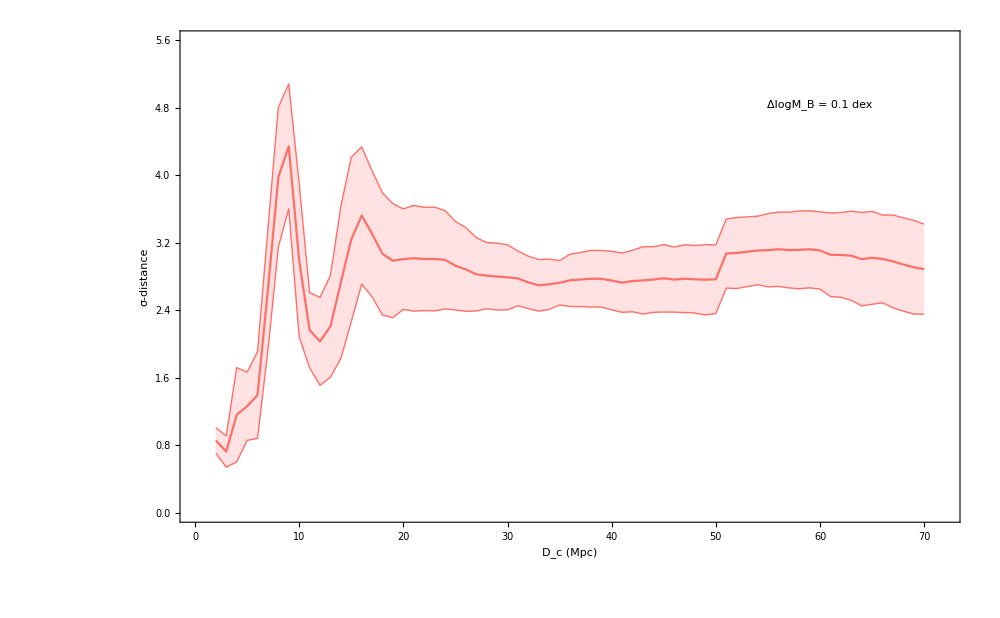

```mathematica
fig2b01=ListLinePlot[tabfin01,IntervalMarkers->"Bands",Frame->True,Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{0,72},{0,5.6}},PlotStyle->{{RGBColor["#ff6f69"]}},ImageSize->1000, FrameStyle -> Directive[Black, Thick],Prolog->Inset[Framed["ΔlogΜ_B = 0.1 dex"],Scaled[{0.82,0.85}]]]
```

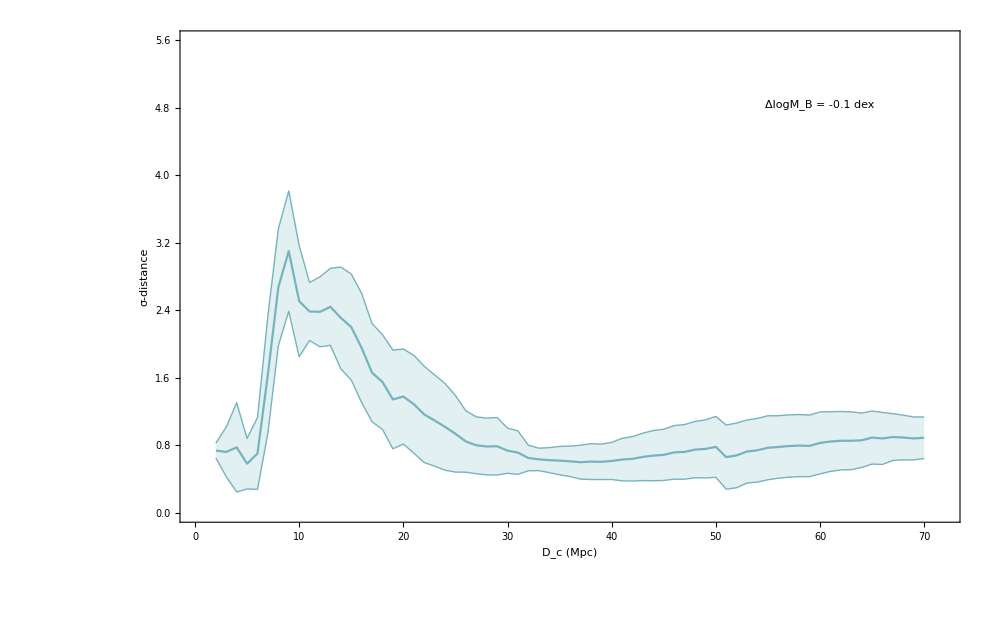

```mathematica
fig2bneg01=ListLinePlot[tabfinneg01,IntervalMarkers->"Bands",Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{0,72},{0,5.6}},PlotStyle->{{RGBColor["#76b4bd"]}},ImageSize->1000, FrameStyle -> Directive[Black, Thick],Frame->{{False,True},{True,True}},Prolog->Inset[Framed["ΔlogΜ_B = -0.1 dex"],Scaled[{0.82,0.85}]]]
```

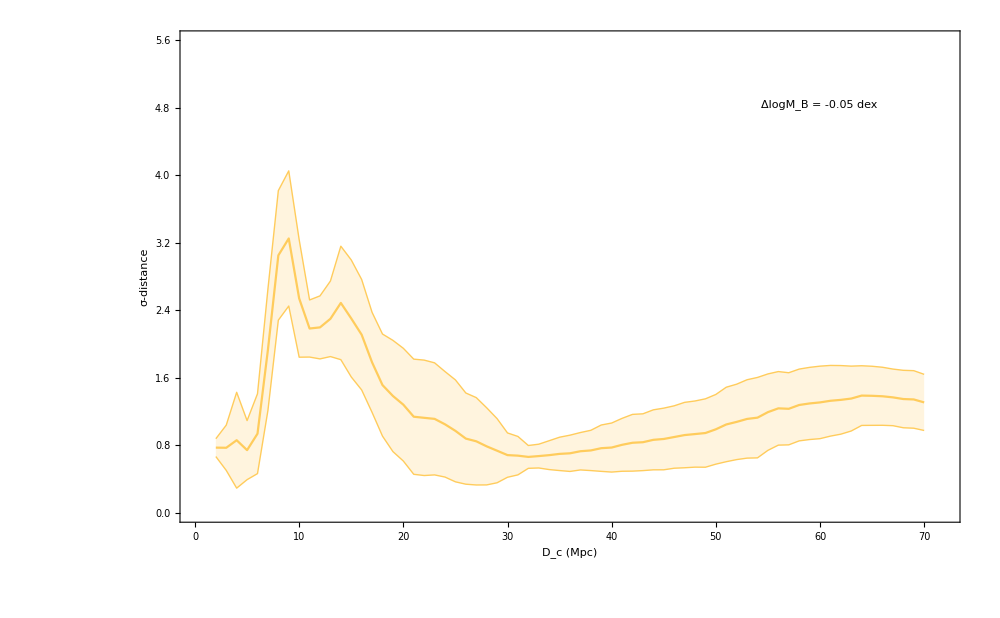

```mathematica
fig2bneg005=ListLinePlot[tabfinneg005,IntervalMarkers->"Bands",Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{0,72},{0,5.6}},PlotStyle->{{RGBColor["#ffcc5c"]}},ImageSize->1000, FrameStyle -> Directive[Black, Thick],Frame->{{False,True},{False,True}},Prolog->Inset[Framed["ΔlogΜ_B = -0.05 dex"],Scaled[{0.82,0.85}]]]
```

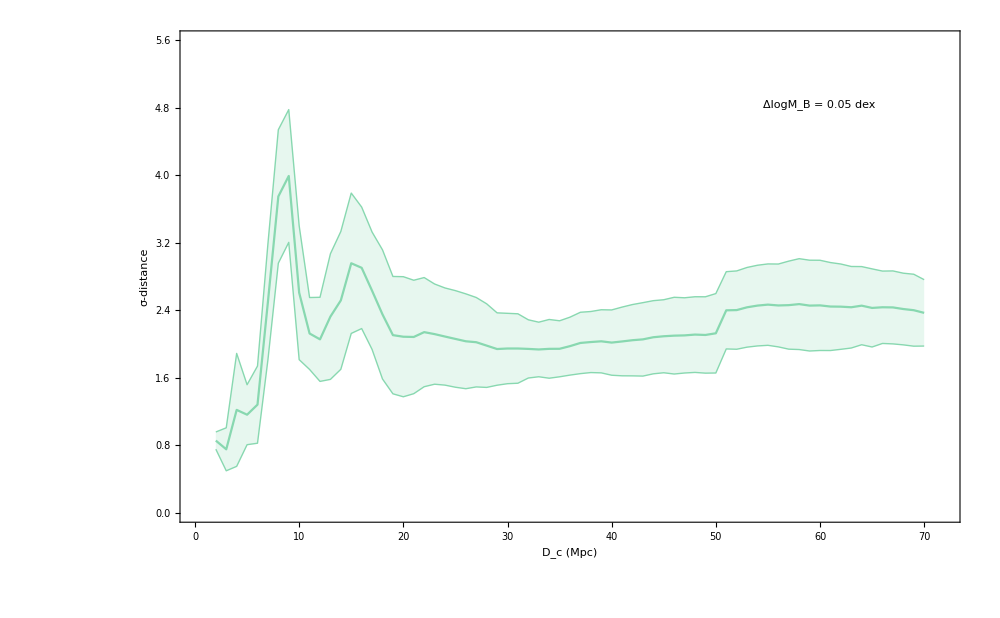

```mathematica
fig2b005=ListLinePlot[tabfin005,IntervalMarkers->"Bands",Joined->True,FrameLabel->{"D_c (Mpc)","σ-distance"},BaseStyle->{Large,FontFamily->"Times",22},LabelStyle->Directive[Black,Large],PlotRange->{{0,72},{0,5.6}},PlotStyle->{{RGBColor["#88d8b0"]}},ImageSize->1000, FrameStyle -> Directive[Black, Thick],Frame->{{True,True},{False,True}},Prolog->Inset[Framed["ΔlogΜ_B = 0.05 dex"],Scaled[{0.82,0.85}]]]
```

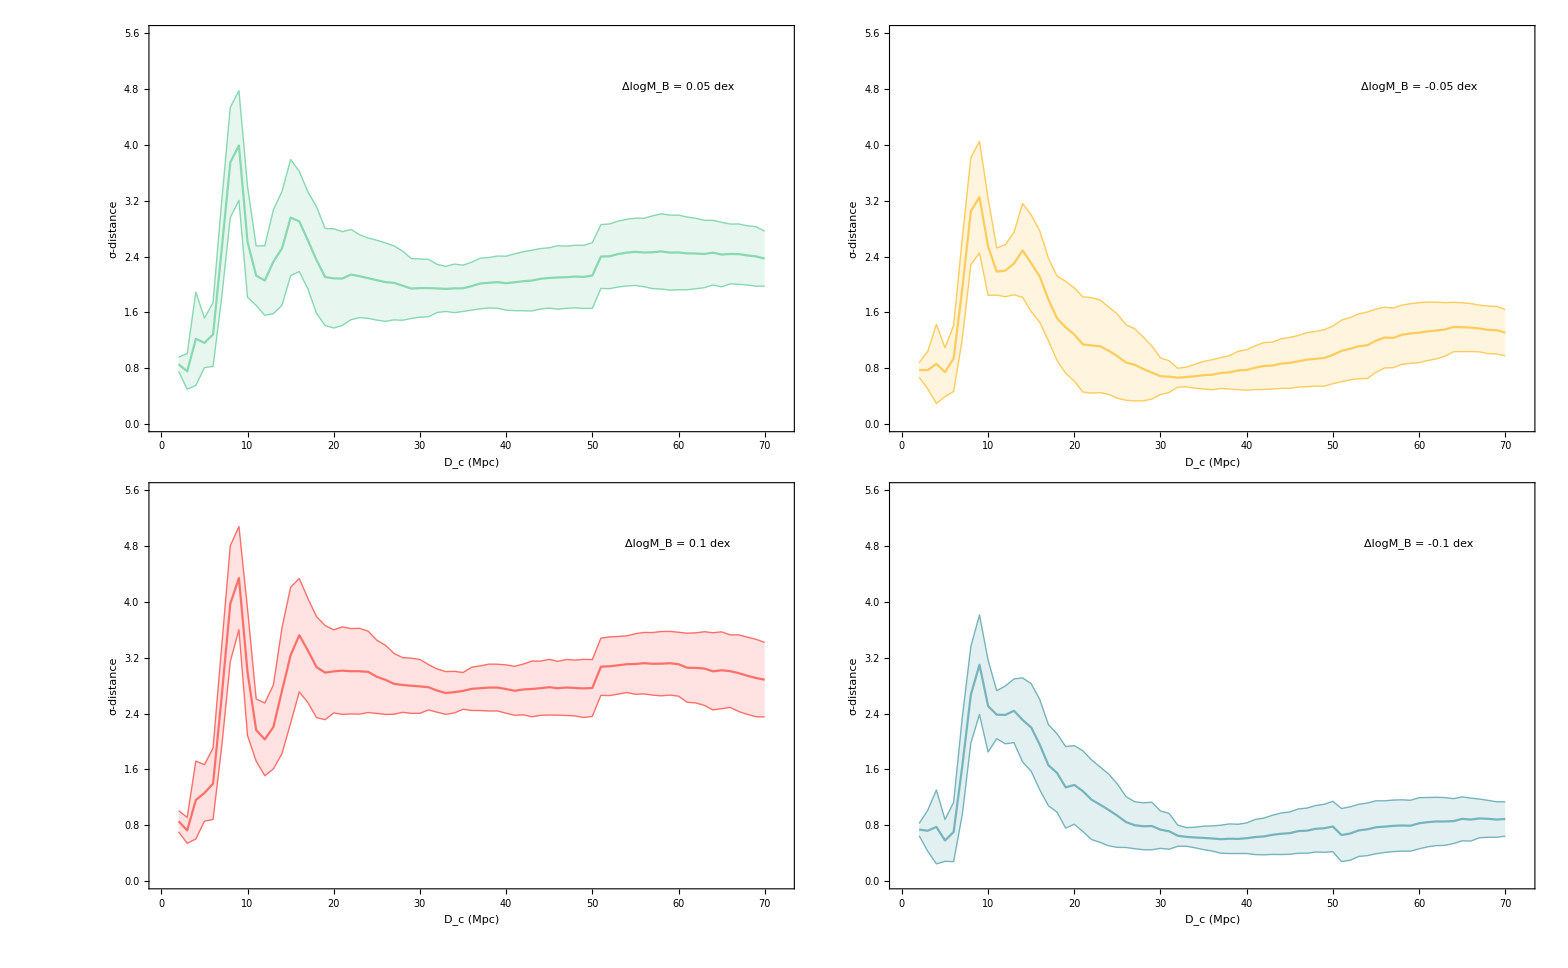

```mathematica
pltfin=GraphicsGrid[{{fig2b005,fig2bneg005},{fig2b01,fig2bneg01}},Spacings->{-105,-65},ImageSize->1900]
```

```mathematica
Export[NotebookDirectory[]<>"figDM.pdf",pltfin,ImageResolution->1000];
```